matrix= (-3/2 | -3/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-3/8 | -3/2 | -3/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -3/8 | -3/2 | -3/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -3/8 | -3/2 | -3/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -3/8 | -3/2 | -3/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -3/8 | -3/2 | -3/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -3/8 | -3/2 | -3/8 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -3/8 | -3/2 | -3/8 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/8 | -3/2 | -3/8 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/8 | -3/2 | -3/8 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/8 | -3/2 | -3/8 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/8 | -3/2 | -3/8 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/8 | -3/2 | -3/8 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/8 | -3/2 | -3/8
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -3/8 | -3/2)

delta= (5.95573
7.14129
7.13335
7.12513
7.11751
7.11079
7.10501
7.10009
7.09592
7.09239
7.0894
7.08687
7.08471
7.08286
8.27229)

a={-12.2,-15.6,-19.5,-23.9,-28.7,-33.9,-39.6,-45.7,-52.3,-59.3,-66.8,-74.7,-83.1,-91.8,-101.,-111.}

b={8.63,9.82,11.,12.2,13.4,14.6,15.8,16.9,18.1,19.3,20.5,21.7,22.9,24.,25.4,25.7}

c={-3.18,-3.18,-3.17,-3.17,-3.17,-3.16,-3.16,-3.16,-3.16,-3.15,-3.15,-3.16,-3.12,-3.27,-2.69,-4.84,3.18}

d={0.0025,-0.00791,-0.00965,-0.00994,-0.00906,-0.00801,-0.00668,-0.00638,-0.0028,-0.0121,0.026,-0.113,0.409,-1.54,5.73,-21.4}

5.×10^-6

5.×10^-7

4.×10^-7

2.×10^-7

2.×10^-7

9.×10^-8

4.×10^-7

9.×10^-7

4.×10^-6

0.00001

0.00006

0.0002

0.0008

0.003

0.01

0.04

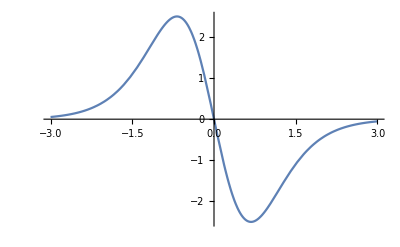

{2.49846,{y→-0.679672}}

0.05

```mathematica
f[x_]:=x^2*ArcTan[7*x/13];
A=-3;
B=3;
n=16;
h=(A-B)/n;
x={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
For[i=1,i≤ n+1,i++,x[[i]]=A+h*(i-1)*1.;]
delta={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
For[i=2,i≤n,i++,delta[[i-1]]=6*(f[x[[i+1]]]-2*f[x[[i]]]+f[x[[i-1]]])/h;]
t=Table[0,{i, n-1},{j,n-1}];
For[i=0,i≤ n-2,i++;t[[i]][[i]]=4*h;];
For[i=1,i≤ n-2,i++;t[[i]][[i-1]]=h;
t[[i-1]][[i]]=h;]
Print["matrix="MatrixForm[t]];
delta[[1]]-=f''[A]*h;
delta[[15]]-=f''[B]*h;
Print["delta="MatrixForm[delta]];
temp=LinearSolve[t,delta];
c={f''[A]*1.,temp[[1]],temp[[2]],temp[[3]],temp[[4]],temp[[5]],temp[[6]],temp[[7]],temp[[8]],temp[[9]],temp[[10]],temp[[11]],temp[[12]],temp[[13]],temp[[14]],temp[[15]],f''[B]*1.};
d={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
For[i=1,i≤n,i++, d[[i]]=(c[[i+1]]-c[[i]])/h]
b={0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0};
For[i=1,i≤n,i++,b[[i]]=h/2*c[[i+1]]-h^2/6*d[[i]]+(f[x[[i+1]]]-f[x[[i]]])/h];
Print["a=",Table[NumberForm[f[x[[i+1]]],3],{i,n}]];
Print["b=",MatrixForm[NumberForm[b,3]]];
Print["c=",MatrixForm[NumberForm[c,3]]];
Print["d=",MatrixForm[NumberForm[d,3]]];
s[y_,i_]:=f[x[[i+1]]]+b[[i]]*(y-x[[i+1]])+c[[i+1]]/2*(y-x[[i+1]])^2+d[[i]]/6*(y-x[[i+1]])^3;
For[i=1,i≤16,i++,Print[NumberForm[Abs[f[A+(i-1)*h+h/2]-s[A+(i-1)*h+h/2,i]],1]];]
Plot[f''''[y],{y,A,B}]
FindMaximum[{f''''[y],A≤y≤ B},{y,A}]
M=2.4984;
R=NumberForm[((B-A)/n)^4*M,1]
```